## Show populations

```mathematica
makePopNormal[]:= RandomVariate[NormalDistribution[0,1],1*^5]

makePopSkew[]:=RandomVariate[SkewNormalDistribution[0,2,4],1*^5]

makePopSuper[]:=(
pdf=ProbabilityDistribution[Exp[(-(x)^4)/2],{x,-Infinity,Infinity}];
RandomVariate[pdf,1*^5]
)

makePopCauchy[]:=RandomVariate[CauchyDistribution[0,1],1*^5]

makePopError[split_,std_]:=RandomVariate[NormalDistribution[0,1],Round[split*1*^5]]~Join~RandomVariate[NormalDistribution[3,std],Round[(1-split)*1*^5]]
```

```mathematica
plotFunc[pop_,label_]:=Histogram[
Select[pop,Abs[#]<5&],
{0.05},
ImageSize->400,
LabelStyle->20,
Frame->True,
PlotLabel->label,
PlotRange->{{-5,5},{0,2500}},
ChartStyle->EdgeForm[None]
]
```

```mathematica
imgArr = {};
```

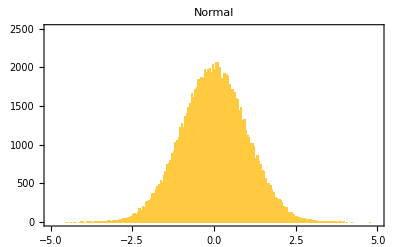

```mathematica
population =makePopNormal[] ;

img = plotFunc[population,"Normal"]

AppendTo[imgArr,img];
```

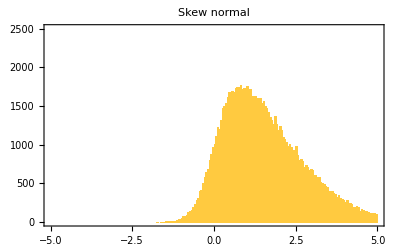

```mathematica
population = makePopSkew[];

img = plotFunc[population,"Skew normal"]

AppendTo[imgArr,img];
```

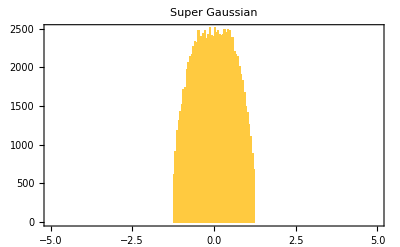

```mathematica
population = makePopSuper[];


img = plotFunc[population,"Super Gaussian"]

AppendTo[imgArr,img];
```

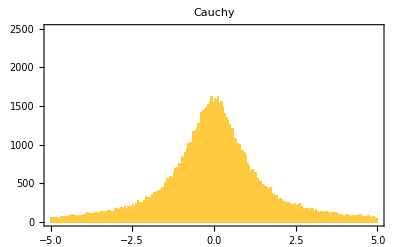

```mathematica
population = makePopCauchy[];


img = plotFunc[population,"Cauchy"]

AppendTo[imgArr,img];
```

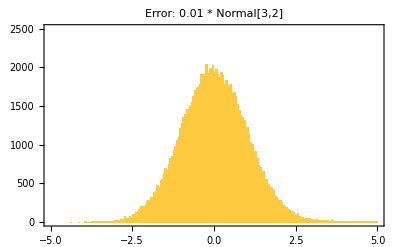

```mathematica
population = makePopError[0.99,2];

img = plotFunc[population,"Error: 0.01 * Normal[3,2]"]

AppendTo[imgArr,img];
```

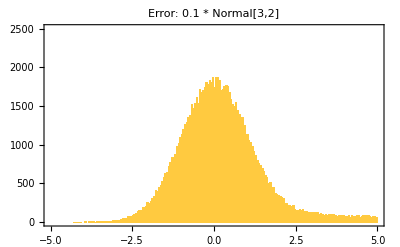

```mathematica
population = makePopError[0.9,2];

img = plotFunc[population,"Error: 0.1 * Normal[3,2]"]

AppendTo[imgArr,img];
```

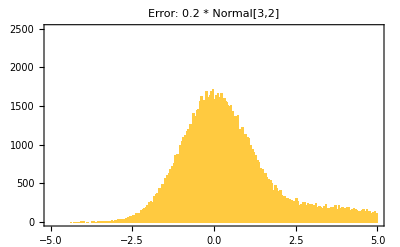

```mathematica
population = makePopError[0.8,2];

img = plotFunc[population,"Error: 0.2 * Normal[3,2]"]

AppendTo[imgArr,img];
```

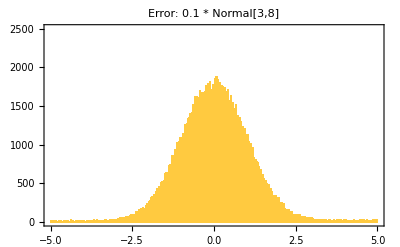

```mathematica
population = makePopError[0.9,8];

img = plotFunc[population,"Error: 0.1 * Normal[3,8]"]

AppendTo[imgArr,img];
```

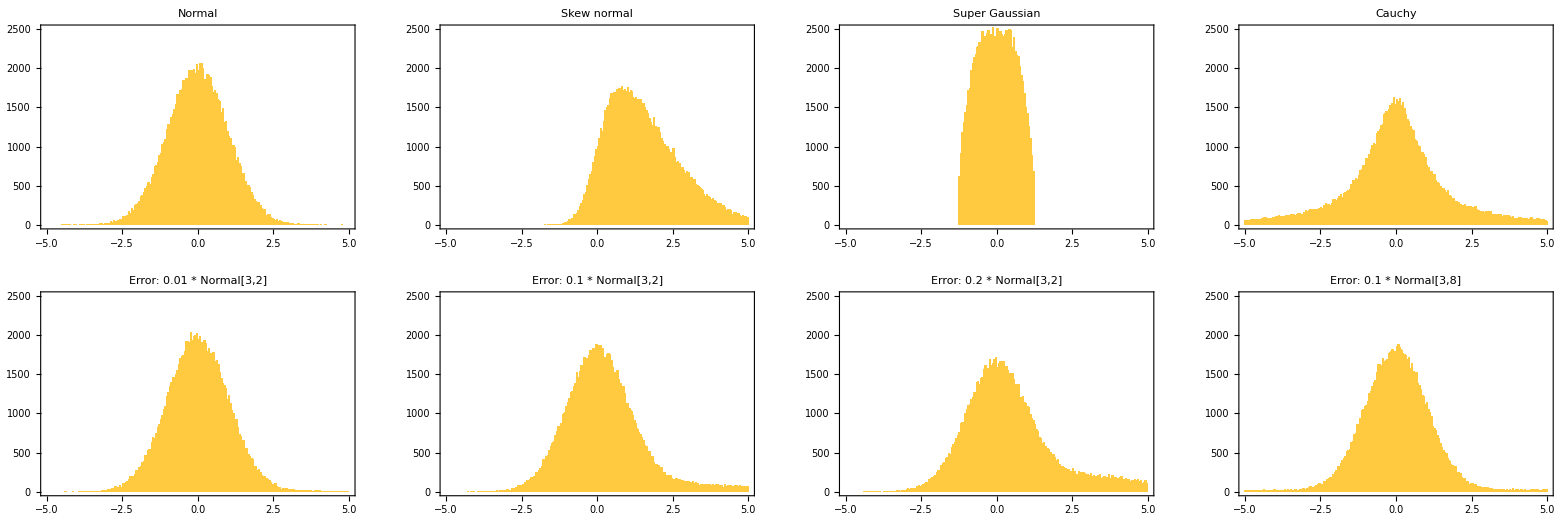

```mathematica
GraphicsGrid[ArrayReshape[imgArr,{2,4}],ImageSize->1600]
```

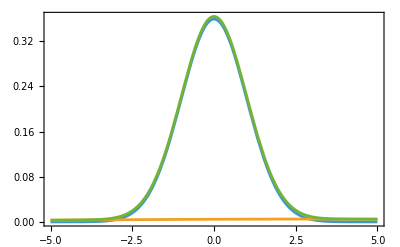

```mathematica
Plot[Evaluate[{
split/((1)√(2π))Exp[(-(x-0)^2)/(2 (1)^2)],
(1-split)/((errorSigma)√(2π))Exp[(-(x-3)^2)/(2 (errorSigma)^2)],
split/((1)√(2π))Exp[(-(x-0)^2)/(2 (1)^2)]+(1-split)/((errorSigma)√(2π))Exp[(-(x-3)^2)/(2 (errorSigma)^2)]
}/.{split->0.9,errorSigma->8}],
{x,-5,5},
ImageSize->400,
Frame->True,
LabelStyle->20,
PlotRangePadding->None
]
```

## Construct all populations

```mathematica
allPopulations = {
Table[makePopNormal[],10],
Table[makePopSkew[],10],
Table[makePopSuper[],10],
Table[makePopCauchy[],10],
Table[makePopError[0.99,2],10],
Table[makePopError[0.9,2],10],
Table[makePopError[0.8,2],10],
Table[makePopError[0.9,8],10]
};
```

## Fit methods

```mathematica
rmsNFunc[pop_,n_]:=(
mean = Mean[pop];
modPop = pop-mean;
modPop = SortBy[modPop, Abs[#]&];



popSubset = modPop[[1;;Round[(n*Length[pop])]]];

(*Print[modPop[[1]],", ",modPop[[-1]]];
Print[popSubset[[1]],", ",popSubset[[-1]]];*)

StandardDeviation[popSubset]
)
```

```mathematica
getFitGaussian[pop_]:=(
binData = CountsBy[pop,Round[#,0.05]&];
binData=Transpose[{Keys[binData],Values[binData]}];
expr = A * Exp[(-(x-x0)^2)/(2 σ^2)]+c;
nlm=NonlinearModelFit[
binData,
{expr,c>=0},
{
{A,2000},
{x0,0.5},
{σ,1.0},
{c,10.0}
},
x,
MaxIterations->1000,
Method->"NMinimize"
];

nlm
)
```

```mathematica
gaussianFitSigma[pop_]:=(
Abs[σ]/.(getFitGaussian[pop])["BestFitParameters"]
)
```

```mathematica
smallestInterval[pop_,n_]:=(
sortedPop = Sort[pop];
k =Round[Length[sortedPop]*n];
minRange = Infinity;

For[i=1,i<Length[sortedPop]-k,i++,
currentRange = sortedPop[[i+k]]-sortedPop[[i]];
If[currentRange<minRange,minRange = currentRange];
];

minRange
)

smallestIntervalImpliedSigma[pop_,n_]:=(
interval = smallestInterval[pop,n];
intervalToSigmaFactor = InverseErf[n]*2*√2;
interval/intervalToSigmaFactor
)
```

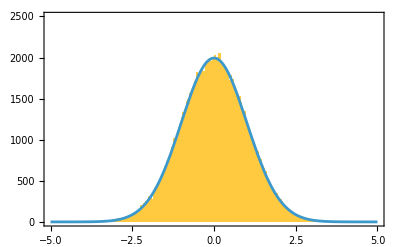
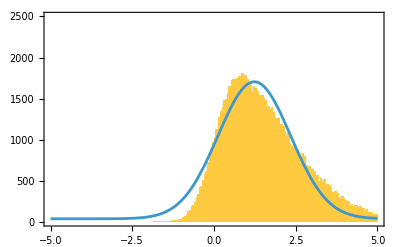
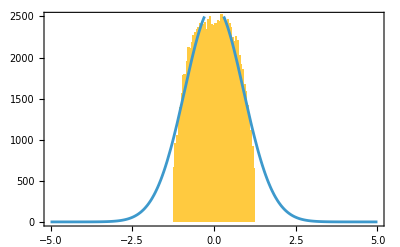
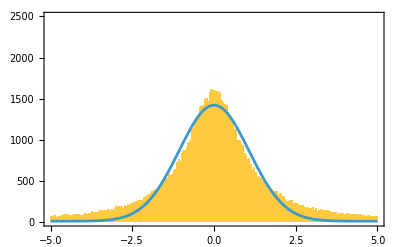
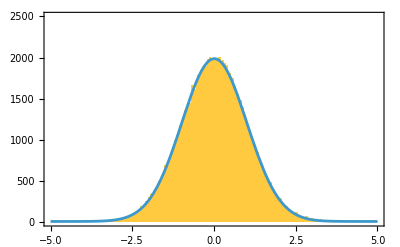
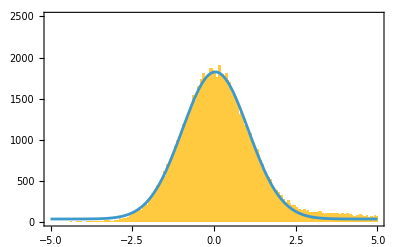
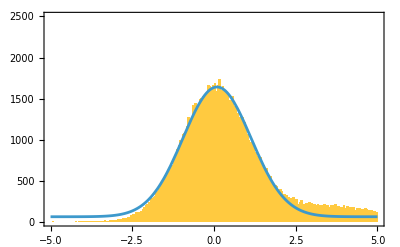
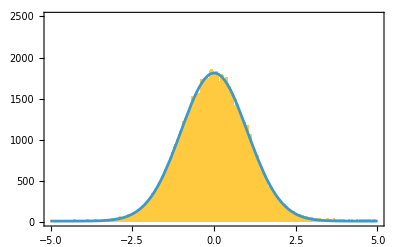

```mathematica
Table[
nlm = getFitGaussian[pop];
Show[
plotFunc[pop,""],
Plot[nlm["BestFit"],{x,-5,5},PlotRange->{0,2500}]
],
{pop,allPopulations[[All,1]]}
]
```

```mathematica
gaussianFitSigma[population]
```

1.00975

```mathematica
smallestIntervalImpliedSigma[population,0.9]
```

1.37697

## Apply fits to populations

```mathematica
exportRow1= Table[
results =rmsNFunc[#,1]&/@row;
ToString[Round[Median[results], 0.001]]<>" ± "<>ToString[Round[ StandardDeviation[results],0.001]],
{row,allPopulations}
]
```

{1. ± 0.002,1.264 ± 0.002,0.631 ± 0.001,253.093 ± 1224.18,1.059 ± 0.003,1.457 ± 0.007,1.745 ± 0.005,2.855 ± 0.009}

```mathematica
exportRow2= Table[
results =rmsNFunc[#,0.9]&/@row;
ToString[Round[Median[results], 0.001]]<>" ± "<>ToString[Round[ StandardDeviation[results],0.001]],
{row,allPopulations}
]
```

{0.789 ± 0.002,0.954 ± 0.002,0.552 ± 0.001,1.893 ± 0.408,0.799 ± 0.003,0.922 ± 0.003,1.125 ± 0.003,0.943 ± 0.002}

```mathematica
exportRow3= Table[
results =gaussianFitSigma[#]&/@row;
ToString[Round[Median[results], 0.001]]<>" ± "<>ToString[Round[ StandardDeviation[results],0.001]],
{row,allPopulations}
]
```

{1. ± 0.004,1.12 ± 0.007,0.899 ± 0.004,1.063 ± 0.005,0.999 ± 0.005,1.014 ± 0.004,1.035 ± 0.005,1.01 ± 0.003}

```mathematica
exportRow4= Table[
results =smallestIntervalImpliedSigma[#,0.9]&/@row;
ToString[Round[Median[results], 0.001]]<>" ± "<>ToString[Round[ StandardDeviation[results],0.001]],
{row,allPopulations}
]
```

{0.999 ± 0.003,1.193 ± 0.003,0.615 ± 0.001,3.837 ± 0.026,1.019 ± 0.003,1.275 ± 0.006,1.67 ± 0.005,1.378 ± 0.007}

```mathematica
exportHeaderRow = {"Normal[0,1]\n","SkewNormal[0,2,4]\n","SuperGaussian[0,1,2]\n","Cauchy[0,1]\n","0.99 * Normal\n + 0.01 * Normal[3,2]","0.9 * Normal\n + 0.1 * Normal[3,2]","0.8 * Normal\n + 0.2 * Normal[3,2]","0.9 * Normal\n + 0.1 * Normal[3,8]"};
```

```mathematica
Style[
TableForm[
Transpose[{exportRow1,exportRow2,exportRow3,exportRow4}],
TableHeadings->{exportHeaderRow,{"RMS 100%","RMS 90%", "Gaussian fit","SIIS 90%"}}
],
FontFamily->"Helvetica",
FontSize->18
]
```

| RMS 100% | RMS 90% | Gaussian fit | SIIS 90%
Normal[0,1]
 | 1. ± 0.002 | 0.789 ± 0.002 | 1. ± 0.004 | 0.999 ± 0.003
SkewNormal[0,2,4]
 | 1.264 ± 0.002 | 0.954 ± 0.002 | 1.12 ± 0.007 | 1.193 ± 0.003
SuperGaussian[0,1,2]
 | 0.631 ± 0.001 | 0.552 ± 0.001 | 0.899 ± 0.004 | 0.615 ± 0.001
Cauchy[0,1]
 | 253.093 ± 1224.18 | 1.893 ± 0.408 | 1.063 ± 0.005 | 3.837 ± 0.026
0.99 * Normal
 + 0.01 * Normal[3,2] | 1.059 ± 0.003 | 0.799 ± 0.003 | 0.999 ± 0.005 | 1.019 ± 0.003
0.9 * Normal
 + 0.1 * Normal[3,2] | 1.457 ± 0.007 | 0.922 ± 0.003 | 1.014 ± 0.004 | 1.275 ± 0.006
0.8 * Normal
 + 0.2 * Normal[3,2] | 1.745 ± 0.005 | 1.125 ± 0.003 | 1.035 ± 0.005 | 1.67 ± 0.005
0.9 * Normal
 + 0.1 * Normal[3,8] | 2.855 ± 0.009 | 0.943 ± 0.002 | 1.01 ± 0.003 | 1.378 ± 0.007